# PSet 3

## Chapter 9

```mathematica
Manipulate[Range[n],{n,0,100}]
```

```mathematica
Manipulate[ListPlot[Range[n]],{n,5,50}]
```

```mathematica
Manipulate[Column[Table[x,n]],{n,1,10}]
```

```mathematica
Manipulate[Graphics[Style[Disk[],Hue[n]]],{n,0,1,0.02}]
```

```mathematica
Manipulate[Graphics[Style[Disk[],RGBColor[r,g,b]]],{r,0,1},{g,0,1},{b,0,1}]
```

```mathematica
Manipulate[IntegerDigits[n],{n,1000,9999,1}]
```

```mathematica
IntegerDigits[9999]
```

{9,9,9,9}

```mathematica
Manipulate[Table[Hue[n],{n,0,1,1/m}],{m,5,50}]
```

```mathematica
Manipulate[PieChart[Table[1,n]],{n,1,10}]
```

```mathematica
Manipulate[BarChart[IntegerDigits[n]],{n,100,999,1}]
```

```mathematica
Manipulate[Table[RandomColor[],n], {n,1,50}]
```

```mathematica
Manipulate[Column[Range[b]^p],{b,1,25},{p,1,10,1}]
```

```mathematica
Manipulate[NumberLinePlot[Range[x]^n],{x,1,10},{n,1,5}]
```

```mathematica
Manipulate[Graphics3D[Style[Sphere[],RGBColor[r,255-r,0]]],{r,0,255}]
```

## Chapter 10

```mathematica
ColorNegate[EdgeDetect[CurrentImage[]]]
```

-Graphics-

```mathematica
Manipulate[Blur[CurrentImage[],n],{n,0,20}]
```

```mathematica
Table[Blur[EdgeDetect[CurrentImage[]],n],{n,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImageCollage[{CurrentImage[],Binarize[CurrentImage[]],ColorNegate[CurrentImage[]],EdgeDetect[CurrentImage[]]}]
```

-Graphics-

```mathematica
ImageAdd[{CurrentImage[],Binarize[CurrentImage[]]}]
```

-Graphics-

```mathematica
Manipulate[Blur[EdgeDetect[CurrentImage[]],n],{n,1,20}]
```

```mathematica
EdgeDetect[Graphics3D[Sphere[]]]
```

-Graphics-

```mathematica
Manipulate[Blur[Graphics[Style[RegularPolygon[5],Purple]],n],{n,0,20}]
```

```mathematica
ImageCollage[Table[Graphics[Style[Disk[],RandomColor[]]],9]]
```

-Graphics-

```mathematica
ImageCollage[Table[Graphics3D[Style[Sphere[],Hue[n]]],{n,0,1,0.2}]]
```

-Graphics-

```mathematica
Table[Blur[Graphics[Disk[]],n],{n,0,30,5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImageAdd[{Graphics[Disk[]],CurrentImage[]}]
```

-Graphics-

```mathematica
ImageAdd[{Graphics[Style[RegularPolygon[8],Red]],CurrentImage[]}]
```

-Graphics-

```mathematica
ImageAdd[{CurrentImage[],ColorNegate[EdgeDetect[CurrentImage[]]]}]
```

-Graphics-

## Chapter 10

```mathematica
StringJoin["hello","hello"]
```

hellohello

```mathematica
StringJoin[ToUpperCase[Alphabet[]]]
```

ABCDEFGHIJKLMNOPQRSTUVWXYZ

```mathematica
StringReverse[StringJoin[Alphabet[]]]
```

zyxwvutsrqponmlkjihgfedcba

```mathematica
StringJoin[Table["AGCT",100]]
```

AGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCT

```mathematica
StringTake[StringJoin[Alphabet[]],6]
```

abcdef

```mathematica
Column[Table[StringTake["This is about strings",n],{n,StringLength["This is about strings"]}]]
```

T
Th
Thi
This
This 
This i
This is
This is 
This is a
This is ab
This is abo
This is abou
This is about
This is about 
This is about s
This is about st
This is about str
This is about stri
This is about strin
This is about string
This is about strings

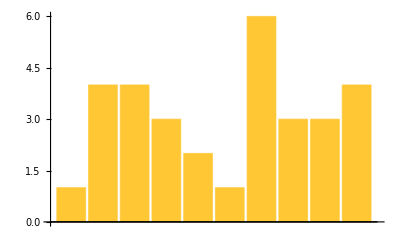

```mathematica
BarChart[StringLength[TextWords["A long time ago in a galaxy far, far away"]]]
```

```mathematica
StringLength[WikipediaData["computer"]]
```

60266

```mathematica
Length[TextWords[WikipediaData["computer"]]]
```

9271

```mathematica
Take[TextSentences[WikipediaData["strings"]],1]
```

{String or strings may refer to:}

```mathematica
StringJoin[StringTake[TextSentences[WikipediaData["computers"]],1]]
```

AMTTACCESEMTTTCTPP=ITTDBTTTT==DTLTTTSITIIDMTTAAATTTIASIBIAITITIITSI=CCAHTFTTTAEBNH=ITax()2{,THI=DHTTTTAB==CBTDETTITIRTZTT=PTEITDTTHACIINCTLOTIIIHBT==TTHTVTE=ECWATIHJTIIAATBAIL=TJFCJTHATHTTWITT=TTDTKIHKNNHPNIMTGFTTWISTITS=TTLTTTT=C=A=SH=TC==ATIET=WTTSC=TSC=TCATRDIRTPIWJSAIT=TES=TTSHTALTSG=AETTLSIETWOAMTTRACrRIIISFIIG=IDOHCIAMA=WTOBItSTBSIT=SMSTSS=SSCICW=T=TTMIAL=TITHTFMPWSTCBOTOI=ITTSTTITMWITC=PUTTS=MF=ATHHIT=PALTP=ETHOBSA=CTITTITCITA"=AWA=TMH=TQCVSLTTT=ACARPE=AT=====M

```mathematica
Max[StringLength[WordList[]]]
```

23

```mathematica
Count[LetterNumber[StringTake[WordList[],1]],17]
```

194

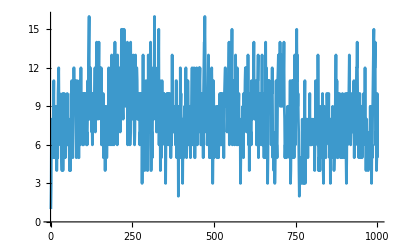

```mathematica
ListLinePlot[StringLength[Take[WordList[],1000]]]
```

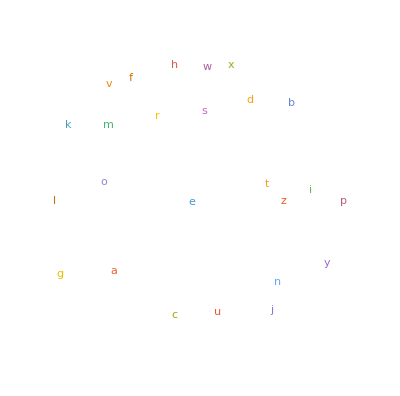

```mathematica
WordCloud[Table[Characters[Part[WordList[],RandomInteger[39176]]],100]] (*Not enough memory to compute for entire wordlist so I just did 100 random words from it*)
```